```mathematica
<<mf22.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
jNew[n_,m_]:=
Module[{ns,collect1,cf,collect2},
ns=Normal[J[n,m]]/.x->(2^6*m^3*x);
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];(* this division by cf might spoil interpolation *)
Return[collect2]]
```

```mathematica
leadingTermCoefficient[polynomial_,x_]:=Module[{degree,leading},
degree=Exponent[polynomial,x];
leading=Coefficient[polynomial,x,degree];
Return[leading]]
```

```mathematica
rationalQ[x_]:=
IntegerQ[Numerator[x]]&&IntegerQ[Denominator[x]]&&!(Denominator[x]==0);
Attributes[rationalQ]=Listable
```

Listable

```mathematica
polyIsConstantQ[polynomial_]:=Module[{tf},
tf=False;
If[rationalQ[polynomial]==True,tf=True];
Return[tf]]
```

```mathematica
polyIsConstantQ[x]
```

False

```mathematica
polyIsConstantQ[3]
```

True

```mathematica
leadingTerm[11*x^2-x+1]
```

11

```mathematica
poly=25*(x-2)^3*(2*x+5)^2*(x^3-x^2-1);
Print[Collect[poly,x]];
fp=Factor[poly];
Print[fp];
ft=FactorTerms[poly,x];
Print[ft];
fl=FactorList[poly];
Print[fl];
ftl=FactorTermsList[poly];
Print[ftl]
```

5000-3500 x+3550 x^2-7325 x^3+2150 x^4+2525 x^5-1075 x^6-200 x^7+100 x^8

25 (-2+x)^3 (5+2 x)^2 (-1-x^2+x^3)

25 (200-140 x+142 x^2-293 x^3+86 x^4+101 x^5-43 x^6-8 x^7+4 x^8)

{{25,1},{-2+x,3},{5+2 x,2},{-1-x^2+x^3,1}}

{25,200-140 x+142 x^2-293 x^3+86 x^4+101 x^5-43 x^6-8 x^7+4 x^8}

#### McKay-Thompson series of type 4A with a(0) = 24 by Michal Somos. From OEIS A097340. (Tested three Somos series for speed.)

```mathematica
mckayThompson[n_]:=SeriesCoefficient[QPochhammer[-q,q^2]^24/q,{q,0,n}]
```

```mathematica
(* testing below code.... *)
fromPolyToNumberTimesMonic[polynomial_]:=
Module[{ltp},
ltp=leadingTermCoefficient[poly,x];
Return[{ltp,Collect[poly/ltp,x]}]]

monicPolynomialQ[polynomial_,x_]:=
Module[{tf},
tf=False;
If[PolynomialQ[polynomial,x]==True&&leadingTermCoefficient[polynomial,x]==1,tf=True];
Return[tf]]

baseConstantQ[pair_]:=
Module[{ttf,bbase},
ttf=False;
bbase=pair[[1]];
If[polyIsConstantQ[bbase]==True,ttf=True];
Return[ttf]
];
baseNotConstantQ[pair_]:=Not[baseConstantQ[pair]];

factorIntoMonics[polynomial_]:=
Module[{factor,factors,nonconstants,
lnf,lnt,lncf,monicfactor,monicfactorbase,monicfactors,numericalterm,k,kk,leadngterm,base,exponent,number,fpntm},
monicfactors={};
factors=FactorList[polynomial];

numericalterm=Select[factors,baseConstantQ];

lnt=Length[numericalterm];
number=Product[numericalterm[[kk,1]]^numericalterm[[kk,2]],{kk,1,lnt}];
nonconstants=Select[factors,baseNotConstantQ];
lncf=Length[nonconstants];
For[k=0,k<lncf,k++;
factor=nonconstants[[k]];
base=factor[[1]];
exponent=factor[[2]];
poly=base^exponent;
fpntm=fromPolyToNumberTimesMonic[poly];
number=number*fpntm[[1]];
AppendTo[monicfactors,fpntm[[2]]]];
Return[Flatten[{number,monicfactors}]]]

fromMonicFactorsToPolynomial[list_]:=
Module[{j,len,poly,base,exponent,pair},
poly=1;
len=Length[list];
For[j=0,j<len,j++;
poly=poly*list[[j]]];
Return[poly]]
```

```mathematica
stream=OpenWrite["run14sept20no1"];
For[m=2,m<302,m++;
jay=jNew[100,m];
Write[stream,{m,jay}]];
Close[stream]
```

run14sept20no1

```mathematica
stream=OpenRead["run14sept20no1"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

300

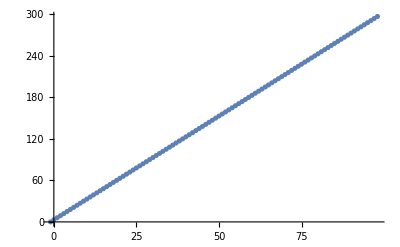

run14sept20no8

```mathematica
stream=OpenRead["run14sept20no1"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run14sept20no8"];
degrees={};
For[n=-2,n<98,n++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]];
ip=InterpolatingPolynomial[data,x];
ip=Expand[ip];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]];
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run14sept20no8"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

100

```mathematica
stream=OpenRead["run14sept20no8"];
list=ReadList[stream];
Close[stream];
yes=0;
no=0;
yes2=0;
no2=0;
For[k=0,k<5,k++;

n=list[[k,1]];
If[n>1,
Print["======================================================================="];
Print["n: ",n];
poly=list[[k,2]];
poly=Collect[poly,x];
Print["poly"];
Print[poly];
Print["poly factored"];
Print[Factor[poly]];
list2=factorIntoMonics[poly];
Print["monic factors"];
Print[list2];
last=Last[list2];
Print["last monic factor"];
Print[last];
If[PolynomialQ[last,x]==True,yes++];
If[PolynomialQ[last,x]==False,no++];
cl=CoefficientList[last,x];
If[AllTrue[cl,rationalQ],yes2++];
If[Not[AllTrue[cl,rationalQ]],no2++]
]
];
Print[{yes,no,yes2,no2}]
```

=======================================================================

n: 2

poly

(131072 x^3)/27+(32768 x^5)/27-(237568 x^7)/27+2048 x^9

poly factored

2048/27 (-2+x) x^3 (2+x) (-16-8 x^2+27 x^4)

monic factors

{2048,-2+x,x^3,2+x,-16/27-(8 x^2)/27+x^4}

last monic factor

-16/27-(8 x^2)/27+x^4

=======================================================================

n: 3

poly

-155136 x^4-51712 x^6+332480 x^8-122272 x^10+11202 x^12

poly factored

2 (-2+x) x^4 (2+x) (19392+11312 x^2-38732 x^4+5601 x^6)

monic factors

{11202,-2+x,x^4,2+x,6464/1867+(11312 x^2)/5601-(38732 x^4)/5601+x^6}

last monic factor

6464/1867+(11312 x^2)/5601-(38732 x^4)/5601+x^6

{2,0,2,0}

```mathematica
stream=OpenRead["run14sept20no8"];
list=ReadList[stream];
Close[stream];
yes1=0;
no1=0;
yes2=0;
no2=0;
yes3=0;
no3=0;
yes4=0;
no4=0;
yes5=0;
no5=0;
yes6=0;
no6=0;
diffs={};
For[j=0,j<100,j++;
Clear[poly];
n=list[[j,1]];
If[n>1,
poly0=list[[j,2]];
list2=factorIntoMonics[poly0];
last=Last[list2];
If[monicPolynomialQ[last,x]==True,yes1++];
If[monicPolynomialQ[last,x]==False,no1++];
If[IrreduciblePolynomialQ[last]==True,yes2++];
If[IrreduciblePolynomialQ[last]==False,no2++];
cl=CoefficientList[last,x];
If[AllTrue[cl,rationalQ],yes3++];
If[Not[AllTrue[cl,rationalQ]],no3++];
test=Collect[mckayThompson[n]*(x-2)*(x+2)*x^(n+1)*last,x];
diff=test-poly0;
diffs=Append[diffs,diff];
If[poly0==test,yes4++];
If[poly0≠test,no4++];
degree=Exponent[last,x];
If[degree==2*n,yes5++];
If[degree≠2*n,no5++];
deglast=Exponent[last,x];
bad=0;
For[k=-1,k<deglast,k++;
cfk=Coefficient[last,x,k];
If[Mod[k,2]==0&&cfk==0,bad++];
If[Mod[k,2]==1&&cfk≠0,bad++]
];
If[bad==0,yes6++];
If[bad≠0,no6++]
]

];
Print[{{yes1,no1},{yes2,no2},{yes3,no3},{yes4,no4},{yes5,no5},{yes6,no6}}];
Print[diffs]
```

{{97,0},{97,0},{97,0},{97,0},{97,0},{97,0}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}